## Some Basic Sound Calculations

```mathematica
zeroDbSpl
```

zeroDbSpl

```mathematica
speedOfSoundMetersPerSec = 343
```

343

```mathematica
cochleaDuctLengthMeters = 30*10^-3
```

3/100

```mathematica
humanHearingRageHz = {20, 20000}
```

{20,20000}

```mathematica
humanHearingRangeSecondsPerCycle = {1.0/humanHearingRageHz[[2]], 1.0/humanHearingRageHz[[1]]}
```

{0.00005,0.05}

```mathematica
zeroDbSplPascals = 20×10^-6
```

1/50000

```mathematica
hearingRangePascals = {zeroDbSplPascals, 20}
```

{1/50000,20}

```mathematica
dBSPL[preasure] = 20×Log[10, preasure/zeroDbSpl]
```

(20 Log[preasure/zeroDbSpl])/Log[10]

```mathematica
humanAmplitudeMaxResolutionDbSpl  = 0.4
```

0.4

```mathematica
samplesRequiredPerWave = 8
```

8

```mathematica
maxSourceTimeResolutionSeconds[sampleRate_] := samplesRequiredPerWave/sampleRate
```

```mathematica
minSourceTimeResolutionSeconds = humanHearingRangeSecondsPerCycle[[2]]
```

0.05

```mathematica
secondsToSampleIndex[sampleRate_, seconds_] := Round[seconds × sampleRate]
```

```mathematica
sampleIndexToSeconds[sampleRate_, index_] := index/sampleRate
```

```mathematica
sampleSizeSecondsDuration = SampleIndexToSeconds
```

SampleIndexToSeconds

```mathematica
sampleSizeSecondsDuration[44100, 8]
```

SampleIndexToSeconds[44100,8]

```mathematica
phoneDurationsSeconds = <|fast->93.9/1000, normal->156.2/1000, slow-> 344.8/1000|>
```

<|fast→0.0939,normal→0.1562,slow→0.3448|>

## A Formula to compute the Mel Frequency of an actual Frequency

```mathematica
MelFrequency[f_] = 2595Log[10,(1+f/700)]
```

(2595 Log[1+f/700])/Log[10]

```mathematica
(2595 Log[1+f/700])/Log[10]
```

(2595 Log[1+f/700])/Log[10]

```mathematica
MelFrequency /@{1000, 3000, 10000, 22000} //N
```

{999.986,1876.45,3073.22,3920.86}

## Import the Sound

```mathematica
utt354 =Import["/home/god/workspace/sdr-work/recordings/audio/3_5_4.wav",  "Data"]
```

{{0.0110172,0.00735496,0.00512711,0.00564592,0.00457778,0.000183111,0.00784326,0.00271615,220485,0.0162358,0.0202033,0.0184942,0.018952,0.016419,0.0195624,0.0195624},{1}}
 |  |  |  |

```mathematica
sampleValueRange[data_] := {Min[data], Max[data]}
```

```mathematica
uttSampleRate = 44100
```

44100

```mathematica
sourceSignalRangeSecondsPerCycle = {MaxSourceTimeResolutionSeconds[uttSampleRate]×1.0, MinSourceTimeResolutionSeconds}
```

{1. MaxSourceTimeResolutionSeconds[44100],MinSourceTimeResolutionSeconds}

## Formula for the number of samples in a given time window

```mathematica
SamplesPerWindow[windowSizeSeconds_, sampleRate_] := Round[windowSizeSeconds × sampleRate]
```

## Formula to partition data at a given time resolution and overlap

### ... at a given time resolution and overlap

```mathematica
timePartitionSamples[data_,sampleRate_, requiredTimeResolution_, requiredTimeOverlap_] := Partition[data, 
SamplesPerWindow[requiredTimeResolution, sampleRate], 
Round[SamplesPerWindow[requiredTimeResolution, sampleRate]-SamplesPerWindow[requiredTimeOverlap, sampleRate]]]
```

```mathematica
timePartitionSamples[utt354[[1]], 44100, 0.0001, 0]
```

{{0.0110172,0.00735496,0.00512711,0.00564592},{0.00457778,0.000183111,0.00784326,0.00271615},55122,{0.018952,0.016419,0.0195624,0.0195624}}
 |  |  |  |

### ... at a given sample window size and overlap

```mathematica
partitionSamples[data_, windowWidth_, windowOverlap_ ] := Partition[data, windowWidth,windowWidth- windowOverlap]
```

```mathematica
partitionSamples[{1,2,3,4,5,6,7}, 2, 0]
```

{{1,2},{3,4},{5,6}}

## Given two vectors we want a formula for the delta vector between them

```mathematica
listSeriesDelta[twosome_:{_List,_List}] := Table[twosome[[2,i]]-twosome[[1,i]], {i, 1, Length[twosome[[1]]]}]
```

```mathematica
test = {{1,2,3,4,5},{3,4,5,6,7}}
```

{{1,2,3,4,5},{3,4,5,6,7}}

```mathematica
listSeriesDelta[test]
```

{2,2,2,2,2}

## A formula that Partitions and deltas a list in one go

This formula deltaPartition partitions the list into pairs which are fed into a listSeriesDelta to obtain the delta values for each pair. The result is a list with elements that are lists of one element so it is flattened into a list of elements half as long as the original list.

```mathematica
deltaForPartition := Flatten[#]& @ Map[listSeriesDelta, #]& @ Partition[#,2]&
```

#### Test the results for Time and Sample partition

```mathematica
deltaForPartition @ partitionSamples[{1,2,3,4,5,6,7}, 1, 0]
```

{1,1,1}

```mathematica
deltaForPartition @ timePartitionSamples [utt354[[1]],44100, 0.0001, 0]
```

{-0.00643941,-0.00717185,0.00271615,-0.00292978,0.00433363,-0.00372326,0.00460829,0.0156865,110233,0.0103153,0.00192267,-0.00521867,0.000305185,0.00106815,0.00817896,-0.000854518}
 |  |  |  |

### Some more parameterized version of the formula

A function that swallows a binary coalescing function and returns a function that can be applied to coalesce a list of values.
NB. Differences is not used here because it goes element by element rather than using disjoint windows

```mathematica
coalesceBinaryPartitions[coalescingFunction_] := Flatten[#]& @ (coalescingFunction @@@ Partition[#,2])&
```

```mathematica
coalesceBinaryPartitions[Plus] @ {1,2,3,4,5,6}
```

{3,7,11}

```mathematica
deltaChange[x_, y_] := Subtract[y,x]
```

```mathematica
coalesceBinaryPartitions[deltaChange] @ {1,2,3,4,5,6}
```

{1,1,1}

## The Single Sample Delta

```mathematica
singleSampleDelta = deltaForPartition @ partitionSamples[utt354[[1]], 1, 0]
```

{-0.00366222,0.000518815,-0.00439467,-0.00512711,0.00219733,-0.00219733,-0.00585955,0.00888089,110234,0.00463881,-0.00909452,-0.00173956,0.00732444,-0.000976592,-0.00170904,-0.00253304,0.}
 |  |  |  |

```mathematica
sampleValueRange[Take[singleSampleDelta,900]]
```

{-0.0139772,0.0130619}

```mathematica
ClusteringComponents[singleSampleDelta]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,110074,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}
 |  |  |  |

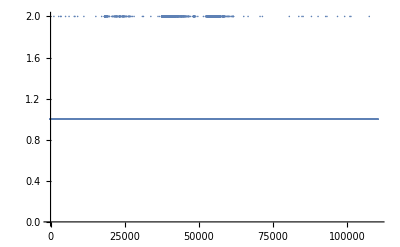

```mathematica
ListPlot[%]
```

## Formulae for Phone detection

```mathematica
speachSpeed ={fast, normal, slow}
```

{fast,normal,slow}

### Mark a List with signal information

```mathematica
markupSameRule =  {l:(x_).. } ->  same[x,instances[{l}]]
```

{l:((x_)..)}→same[x,instances[{l}]]

```mathematica
markupInstancesRuleOld := instances[t_] -> instances[toBeEvaluated[Length][t]]
```

```mathematica
markupInstancesRule := (instances[t_] -> instances[toBeEvaluated[#][t]]) &
```

```mathematica
MarkSignals[dataList_] := Split[ClusteringComponents[dataList]]/. markupSameRule
```

```mathematica
singleSampleMarkedSignals = MarkSignals[singleSampleDelta] /. markupInstancesRule[Length]
```

{same[1,instances[toBeEvaluated[Length][{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,991,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}]]],3128}
 |  |  |  |

### Reduce all signal that can not possibly be a Phone to Noise

The Following assumptions are made:

Phones will maintain signal in a single frequency band for the length of the phone.

Frequency switches occur between phones and not within then

```mathematica
execPendingHeadsRule := toBeEvaluated[h_] ->  h
```

```mathematica
detectPhones[phoneSampleWidth_] := {same[_,instances[size_]] /; size<phoneSampleWidth -> same[noise[minSamplesPerSignal], instances[size]],
same[_,instances[size_]] /; size>=phoneSampleWidth -> same[phone[minSamplesPerSignal], instances[size]]}
```

```mathematica
secondsToSampleIndex[44100, PhoneDurationSeconds[fast]]
```

Round[44100 PhoneDurationSeconds[fast]]

```mathematica
cleanSingleSampleinstances = singleSampleMarkedSignals /.execPendingHeadsRule/. detectPhones[SecondsToSampleIndex[44100, PhoneDurationSeconds[fast]]]
```

{same[1,instances[1134]],same[2,instances[1]],same[1,instances[1628]],same[2,instances[1]],same[1,instances[637]],same[2,instances[1]],same[1,instances[174]],same[2,instances[1]],3114,same[1,instances[1772]],same[2,instances[1]],same[1,instances[329]],same[2,instances[1]],same[1,instances[6192]],same[2,instances[1]],same[1,instances[2764]]}
 |  |  |  |

```mathematica
markupSameInstanceTypesRule = {l:same[x_,instances[_]]..}  ->  same[x, instances[{l}]]
```

{l:(same[x_,instances[_]]..)}→same[x,instances[{l}]]

```mathematica
typeOfInstance =  (# /. same[x_,instances[_]] -> x)&
```

#1/.same[x_,instances[_]]→x&

```mathematica
partitionByInstanceType = Curry[SplitBy][typeOfInstance]
```

Curry[SplitBy][#1/.same[x_,instances[_]]→x&]

```mathematica
grouped = partitionByInstanceType @ cleanSingleSampleinstances /. markupSameInstanceTypesRule
```

{same[1,instances[{same[1,instances[1134]]}]],same[2,instances[{same[2,instances[1]]}]],same[1,instances[{same[1,instances[1628]]}]],same[2,instances[{same[2,instances[1]]}]],3122,same[1,instances[{same[1,instances[6192]]}]],same[2,instances[{same[2,instances[1]]}]],same[1,instances[{same[1,instances[2764]]}]]}
 |  |  |  |

```mathematica
coalesceQuantifiedInstances[x_:same[t_,instances[_Integer]],y_:same[t_,instances[_Integer]]] := {x,y} /. {same[first_,instances[xc_]],same[_,instances[yc_]]} -> same[first, instances[xc+yc]]
```

```mathematica
cleanupRule = same[_, instances[x_Integer]] -> x
```

same[_,instances[x_Integer]]→x

```mathematica
dirty =grouped /. markupInstancesRule[Fold[ coalesceQuantifiedInstances]] /. execPendingHeadsRule /. cleanupRule
```

{same[1,instances[1134]],same[2,instances[1]],same[1,instances[1628]],same[2,instances[1]],same[1,instances[637]],same[2,instances[1]],same[1,instances[174]],same[2,instances[1]],3114,same[1,instances[1772]],same[2,instances[1]],same[1,instances[329]],same[2,instances[1]],same[1,instances[6192]],same[2,instances[1]],same[1,instances[2764]]}
 |  |  |  |

## Detect The Phones along the other lanes

Given that the fastest Phone lasts for..

```mathematica
phoneDurationSeconds[fast]
```

phoneDurationSeconds[fast]

seconds. This is equivalent to

```mathematica
secondsToSampleIndex[44100, phoneDurationSeconds[fast]]
```

Round[44100 phoneDurationSeconds[fast]]

samples. It is pointless to take deltas at this order of magnitude.Our sences notice change and not absolute value. they compare what is happening now to what happened earlier. the first thing they will be able to detect is the value {a2-a1}. Once this is detected they can then detect {a3-a2} and so on. Once a difference is detected the process of detection consumes the two samples and outputs the delta. None of the samples is available for further comparison. The process of measurement consumes the measured. So when the next sample arrives (i.e. a3) we can either:
-  consume it along with the result of the delta before 
or 
- we can compare it with the sample ahead to get a delta with the same semantics as the result before that can be compared with the result before
I propose that the sum of two detected deltas is an indication of the happenings at a longer wavelength (lower frequency). If a second hierarchy of transducers taps into the output of the first layer it can detect (a4-a3)-(a2-a1) as a measured point and feed that down. this layer supplies the lower frequency information to the brain along another line and is tapped by yet another hierarchy level which detects even lower wavelengths and so on. 
If this is so we shall have many lines in the high frequency feeds and fewer in the low frequency feeds however we know for a fact that our ears are more sensitive in the lower frequencies to change than they are in the higher frequencies. But... is sensitivity equal to the density of streams or can we make it equal to the number of measurements that constitute a wavelet detection?
Supposing we do not take deltas of deltas and simply shift the window across. In that case longer wavelengths will have more measurements taken to determine them than shorter (higher frequency) ones. In this case we are obtaining correlations between wavelets (windows) containing more and more samples each. Simply adding lower level measurements can get us here. But the question is what should be the overlap if any? and why?
With no overlap we are doing a straight correlation of successive wavelets at this resolution.
With overlap we mix in some lower levels into the measurement of the higher ones, but we already have these in the lower streams.
I propose that we take no overlap. This allows the measurement of the lower frequencies to be more  precise and to exclude all the levels below. i.e.{a6,a7,a8,a9,a10} - {a1,a2,a3,a4,a5} = {a6-a1, a7-a2, a8-a3, a9-a4, a10-a5} which effactively halves the data points in the same way as the first delta. In this was all streams are made up of exactly half as many data points.

To detect frequencies of 20hz we need to compare windows that are 1/50th of a second.

```mathematica
secondsToSampleIndex[44100, 1/50]
```

882

Windows need to be that many samples wide. But our fastest Phone is 1414 samples wide so

```mathematica
1414/882 //N
```

1.60317

Remember... we said we are not overlapping! So by detecting long wavelengths at this accuracy we risk not being able to see the phone because the jump  is so big. In fact, The fast phone comes up as one transduction measurement at this level. Higher levels will more frequently compare regions that should not be compared. All this given we should keep the level low enough to get enough some character describing the fast Phone but high enough to actually measure this character’s wave variation. 4 measurements sounds arbitrary but maps to about 20ms when considering the 90ms fast Phone. That is 1/50th of a second and 882 samples as calculated above.

The 882nd detection lane will move at 50 measurements per second. while the initial 2 sample lane moves at 22 thousand measurements per second. (remember... we banned overlap!). The 1 measurement at the top of the pyramid is like context for those longer lanes below.

NB progressing to obtain new lanes by adding elements in pevious lanes takes us forward in powers of 2 so we shall have

```mathematica
Log[2,882] // N
```

9.78463

lanes. this skips more lanes at the lower frequencies but drastically makes computation more feasible. with only 10 lanes. Make the number of lanes and algorithm of lane indexing a parameter to investigate the pros/cons but start with the lower number of lanes to get the formulas right without trashing your laptop ;-)

### Lets do the work now

#### Formula to determine the relevant Lanes

```mathematica
lanes=.
```

```mathematica
lanes[sampleRate_Integer, minimumPhoneDurationSeconds_] :=Table[lane[2^i], {i,0,Ceiling[Log[2,secondsToSampleIndex[minimumPhoneDurationSeconds, sampleRate]]]}]
```

```mathematica
lanes[44100, 1/50]
```

{lane[1],lane[2],lane[4],lane[8],lane[16],lane[32],lane[64],lane[128],lane[256],lane[512],lane[1024]}

#### Formula to fill the lanes

```mathematica
seedDeltas = coalesceBinaryPartitions[deltaChange] @ utt354[[1]]
```

{-0.00366222,0.000518815,-0.00439467,-0.00512711,0.00219733,-0.00219733,-0.00585955,0.00888089,110235,-0.00909452,-0.00173956,0.00732444,-0.000976592,-0.00170904,-0.00253304,0.}
 |  |  |  |

```mathematica
laneConstructionRule[data] := lane[i_Integer] -> {}
```

```mathematica
markUpTheData := seedDeltas_ -> MarkSignals[singleSampleDelta] /. markupInstancesRule[Length]
```

```mathematica
cleanSingleSampleinstances = seedDeltas /. markUpTheData /.execPendingHeadsRule/. detectPhones[secondsToSampleIndex[44100, phoneDurationsSeconds[fast]]]
```

{same[noise[minSamplesPerSignal],instances[1134]],same[noise[minSamplesPerSignal],instances[1]],same[noise[minSamplesPerSignal],instances[1628]],3123,same[phone[minSamplesPerSignal],instances[6192]],same[noise[minSamplesPerSignal],instances[1]],same[noise[minSamplesPerSignal],instances[2764]]}
 |  |  |  |

```mathematica
partitionByInstanceType[seedDeltas /. markUpTheData /.execPendingHeadsRule/. detectPhones[secondsToSampleIndex[44100, phoneDurationsSeconds[fast]]]] /. markupSameInstanceTypesRule /. markupInstancesRule[Fold[ coalesceQuantifiedInstances]] /. execPendingHeadsRule /. cleanupRule
```

{same[noise[minSamplesPerSignal],instances[71453]],same[phone[minSamplesPerSignal],instances[9067]],same[noise[minSamplesPerSignal],instances[20773]],same[phone[minSamplesPerSignal],instances[6192]],same[noise[minSamplesPerSignal],instances[2765]]}

```mathematica
partitionByInstanceType[# /. markUpTheData /.execPendingHeadsRule/. detectPhones[secondsToSampleIndex[44100, phoneDurationsSeconds[fast]]]] /. markupSameInstanceTypesRule /. markupInstancesRule[Fold[ coalesceQuantifiedInstances]] /. execPendingHeadsRule /. cleanupRule & @ seedDeltas
```

{same[noise[minSamplesPerSignal],instances[71453]],same[phone[minSamplesPerSignal],instances[9067]],same[noise[minSamplesPerSignal],instances[20773]],same[phone[minSamplesPerSignal],instances[6192]],same[noise[minSamplesPerSignal],instances[2765]]}

### We now have a formula to obtain phone signals from a lane

```mathematica
phoneSignals = partitionByInstanceType[# /. markUpTheData /.execPendingHeadsRule/. detectPhones[secondsToSampleIndex[44100, phoneDurationsSeconds[fast]]]] /. markupSameInstanceTypesRule /. markupInstancesRule[Fold[ coalesceQuantifiedInstances]] /. execPendingHeadsRule /. cleanupRule &
```

partitionByInstanceType[#1/.markUpTheData/.execPendingHeadsRule/.detectPhones[secondsToSampleIndex[44100,phoneDurationsSeconds[fast]]]]/.markupSameInstanceTypesRule/.markupInstancesRule[Fold[coalesceQuantifiedInstances]]/.execPendingHeadsRule/.cleanupRule&

```mathematica
phoneSignals[seedDeltas]
```

{same[noise[minSamplesPerSignal],instances[71453]],same[phone[minSamplesPerSignal],instances[9067]],same[noise[minSamplesPerSignal],instances[20773]],same[phone[minSamplesPerSignal],instances[6192]],same[noise[minSamplesPerSignal],instances[2765]]}

```mathematica
phoneSignals[coalesceBinaryPartitions[deltaChange] @ utt354[[1]]]
```

{same[noise[minSamplesPerSignal],instances[71453]],same[phone[minSamplesPerSignal],instances[9067]],same[noise[minSamplesPerSignal],instances[20773]],same[phone[minSamplesPerSignal],instances[6192]],same[noise[minSamplesPerSignal],instances[2765]]}

### We also have a formula to obtain all of the initial lane data

```mathematica
laneData=.
```

```mathematica
laneData[data_] :=  NestList[coalesceBinaryPartitions[deltaChange] , 
data,
Length[lanes[44100, 1/50]]
]
```

```mathematica
utt354[[1]]
```

{0.0110172,0.00735496,0.00512711,0.00564592,0.00457778,0.000183111,0.00784326,0.00271615,220484,0.0172124,0.0162358,0.0202033,0.0184942,0.018952,0.016419,0.0195624,0.0195624}
 |  |  |  |

```mathematica
laneData[utt354[[1]]]
```

{{0.0110172,0.00735496,0.00512711,0.00564592,0.00457778,0.000183111,0.00784326,0.00271615,220485,0.0162358,0.0202033,0.0184942,0.018952,0.016419,0.0195624,0.0195624},10,{1}}
 |  |  |  |

```mathematica
lanes[44100, 1/50]
```

{lane[1],lane[2],lane[4],lane[8],lane[16],lane[32],lane[64],lane[128],lane[256],lane[512],lane[1024]}

```mathematica
additionKernalsRules = {lane[x_/;x≥1] -> lane[x][kernel @@ {IntegerDigits[2^x+1,2]}],lane[x_/;x<1]->lane[x][kernel[{1}]]}
```

{lane[x_/;x≥1]→lane[x][kernel[IntegerDigits[1+2^x,2]]],lane[x_/;x<1]→lane[x][kernel[{1}]]}

```mathematica
convertAddToSubtractKernelRule = {y__Integer,x_Integer} ->  {y,-x}
```

{y__Integer,x_Integer}→{y,-x}

```mathematica
markupDeltaKernals[lanes_] := lanes /.additionKernalsRules /. convertAddToSubtractKernelRule
```

```mathematica
lanesWithkernels = markupDeltaKernals[lanes[44100, 1/50]]
```

{lane[1][kernel[{1,-1}]],lane[2][kernel[{1,0,-1}]],lane[4][kernel[{1,0,0,0,-1}]],lane[8][kernel[{1,0,0,0,0,0,0,0,-1}]],lane[16][kernel[{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1}]],lane[32][kernel[{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1}]],lane[64][kernel[{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1}]],lane[128][kernel[{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1}]],lane[256][kernel[{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1}]],lane[512][kernel[{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1}]],lane[1024][kernel[{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1}]]}

```mathematica
{lane[0][kernel[{1}]],lane[1][kernel[{1,-1}]],lane[2][kernel[{1,0,-1}]],lane[4][kernel[{1,0,0,0,-1}]]} /. lane[l_][kernel[k_/;Length[#]<l]] :>  ListConvolve[k,{1,2,3,4,5,5,4,7,8,9}]
```

{lane[0][kernel[{1}]],lane[1][kernel[{1,-1}]],lane[2][kernel[{1,0,-1}]],lane[4][kernel[{1,0,0,0,-1}]]}

```mathematica
laneDataSkipList=.
```

```mathematica
laneDataSkipList[data_] := lanesWithkernels /. lane[l_][kernel[k_]] :>  ListConvolve[k, data]/; Length[k]<Length[data]
```

```mathematica
laneDataSkipList[{1,2,3,4,5,5,4,7,8,9}]  /. lane[_][kernel[_]] -> Nothing
```

{{1,1,1,1,0,-1,3,1,1},{2,2,2,1,-1,2,4,2},{4,3,1,3,3,4},{7,7}}

### Formula to get all the signal data

```mathematica
allSignals = phoneSignals /@ laneData[utt354[[1]]]
```

{{same[noise[minSamplesPerSignal],instances[71453]],same[phone[minSamplesPerSignal],instances[9067]],same[noise[minSamplesPerSignal],instances[20773]],same[phone[minSamplesPerSignal],instances[6192]],same[noise[minSamplesPerSignal],instances[2765]]},{same[noise[minSamplesPerSignal],instances[71453]],same[phone[minSamplesPerSignal],instances[9067]],same[noise[minSamplesPerSignal],instances[20773]],same[phone[minSamplesPerSignal],instances[6192]],same[noise[minSamplesPerSignal],instances[2765]]},{same[noise[minSamplesPerSignal],instances[71453]],same[phone[minSamplesPerSignal],instances[9067]],same[noise[minSamplesPerSignal],instances[20773]],same[phone[minSamplesPerSignal],instances[6192]],same[noise[minSamplesPerSignal],instances[2765]]},{same[noise[minSamplesPerSignal],instances[71453]],same[phone[minSamplesPerSignal],instances[9067]],same[noise[minSamplesPerSignal],instances[20773]],same[phone[minSamplesPerSignal],instances[6192]],same[noise[minSamplesPerSignal],instances[2765]]},{same[noise[minSamplesPerSignal],instances[71453]],same[phone[minSamplesPerSignal],instances[9067]],same[noise[minSamplesPerSignal],instances[20773]],same[phone[minSamplesPerSignal],instances[6192]],same[noise[minSamplesPerSignal],instances[2765]]},{same[noise[minSamplesPerSignal],instances[71453]],same[phone[minSamplesPerSignal],instances[9067]],same[noise[minSamplesPerSignal],instances[20773]],same[phone[minSamplesPerSignal],instances[6192]],same[noise[minSamplesPerSignal],instances[2765]]},{same[noise[minSamplesPerSignal],instances[71453]],same[phone[minSamplesPerSignal],instances[9067]],same[noise[minSamplesPerSignal],instances[20773]],same[phone[minSamplesPerSignal],instances[6192]],same[noise[minSamplesPerSignal],instances[2765]]},{same[noise[minSamplesPerSignal],instances[71453]],same[phone[minSamplesPerSignal],instances[9067]],same[noise[minSamplesPerSignal],instances[20773]],same[phone[minSamplesPerSignal],instances[6192]],same[noise[minSamplesPerSignal],instances[2765]]},{same[noise[minSamplesPerSignal],instances[71453]],same[phone[minSamplesPerSignal],instances[9067]],same[noise[minSamplesPerSignal],instances[20773]],same[phone[minSamplesPerSignal],instances[6192]],same[noise[minSamplesPerSignal],instances[2765]]},{same[noise[minSamplesPerSignal],instances[71453]],same[phone[minSamplesPerSignal],instances[9067]],same[noise[minSamplesPerSignal],instances[20773]],same[phone[minSamplesPerSignal],instances[6192]],same[noise[minSamplesPerSignal],instances[2765]]},{same[noise[minSamplesPerSignal],instances[71453]],same[phone[minSamplesPerSignal],instances[9067]],same[noise[minSamplesPerSignal],instances[20773]],same[phone[minSamplesPerSignal],instances[6192]],same[noise[minSamplesPerSignal],instances[2765]]},{same[noise[minSamplesPerSignal],instances[71453]],same[phone[minSamplesPerSignal],instances[9067]],same[noise[minSamplesPerSignal],instances[20773]],same[phone[minSamplesPerSignal],instances[6192]],same[noise[minSamplesPerSignal],instances[2765]]}}

### The Skip-One Sample Delta

```mathematica
skipOneSampleDelta = DeltaForPartition @ PartitionSamples[singleSampleDelta, 1, 0]
```

DeltaForPartition[PartitionSamples[{-0.00366222,0.000518815,-0.00439467,-0.00512711,0.00219733,-0.00219733,-0.00585955,110237,-0.00173956,0.00732444,-0.000976592,-0.00170904,-0.00253304,0.},1,0]]
 |  |  |  |

```mathematica
{{DeltaForPartition[PartitionSamples[{-0.003662221137119664,0.0005188146610919523,-0.004394665364543596,-0.005127109591967529,0.002197332682271798,-0.002197332682271798,-0.005859553819391462,110237,-0.0017395550401318408,0.007324442274239328,-0.0009765923032319102,-0.0017090365306558428,-0.0025330362865077644,0.},1,0]]}, {{{, , , , }}}}
```

```mathematica
SampleValueRange[skipOneSampleDelta]
```

SampleValueRange[DeltaForPartition[PartitionSamples[{-0.00366222,0.000518815,-0.00439467,-0.00512711,0.00219733,-0.00219733,110238,-0.00173956,0.00732444,-0.000976592,-0.00170904,-0.00253304,0.},1,0]]]
 |  |  |  |

```mathematica
SampleValueRange[Take[skipOneSampleDelata,900]]
```

Take::normal: Nonatomic expression expected at position 1 in Take[skipOneSampleDelata,900].

SampleValueRange[Take[skipOneSampleDelata,900]]

```mathematica
ClusteringComponents[skipOneSampleDelata]
```

ClusteringComponents::nosup: ClusteringComponents does not support this type of data.

ClusteringComponents[skipOneSampleDelata]

```mathematica
ListPlot[%92]
```

ListPlot::lpn: -0.0126652 is not a list of numbers or pairs of numbers.

ListPlot[-0.0126652]

replace elements with their representative/symbol upon identification

ClusteringComponents identifies into clusters (i.e. 1,2,3) based on nearness algorithm

samenessPatternComponent takes 1 or more pattern producing as many classes plus a class for those that do not match any of the provided patterns

perform invariant transformations to norm the object(reduce superfluous data points e.g. for time dimension invariances, reduce the time extent) then if it is the first object - add it to the identities list. if it is not (the list has elements) thenuse a distance measure (e.g hamming) to see if it has a representative id, if so then replace it with that symbol. if not create a new id and symbol for it and replace it with that

NB:a pattern is just a description of an invariant transformation. can the third above just be a pattern?

group identity list into lists of contiguous same elements

convert the lists into a same[id, instances[_]] structure

## A Formula to metadata head signals

```mathematica
ClusteringComponents[utt354[[1]],3]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,220324,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}
 |  |  |  |

```mathematica
ListPlot[%78]
```

-Graphics-

```mathematica
ClusteringComponents[utt354[[1]],3]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,220324,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}
 |  |  |  |

```mathematica
ListPlot[%80]
```

ListPlot::lpn: Null is not a list of numbers or pairs of numbers.

ListPlot[Null]

## Computing a few deltas

```mathematica
utt354[[1]]
```

{0.0110172,0.00735496,0.00512711,0.00564592,0.00457778,0.000183111,0.00784326,0.00271615,220484,0.0172124,0.0162358,0.0202033,0.0184942,0.018952,0.016419,0.0195624,0.0195624}
 |  |  |  |

```mathematica
ClusteringComponents[utt354[[1]]]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,220324,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}
 |  |  |  |

```mathematica
ListPlot[%]
```

-Graphics-

```mathematica
SampleValueRange[utt354[[1]]]
```

SampleValueRange[{0.0110172,0.00735496,0.00512711,0.00564592,0.00457778,0.000183111,0.00784326,0.00271615,220485,0.0162358,0.0202033,0.0184942,0.018952,0.016419,0.0195624,0.0195624}]
 |  |  |  |

```mathematica
ThousandSampleDelta = DeltaForPartition @ PartitionSamples[utt354[[1]], 1000, 0]
```

DeltaForPartition[PartitionSamples[{0.0110172,0.00735496,0.00512711,0.00564592,0.00457778,0.000183111,0.00784326,220486,0.0162358,0.0202033,0.0184942,0.018952,0.016419,0.0195624,0.0195624},1000,0]]
 |  |  |  |

```mathematica
SampleValueRange[Take[ThousandSampleDelta,10]]
```

Take::take: Cannot take positions 1 through 10 in DeltaForPartition[PartitionSamples[{0.0110172,0.00735496,0.00512711,0.00564592,0.00457778,0.000183111,0.00784326,0.00271615,«36»,0.00167852,-0.0000915527,0.0151372,0.00717185,0.00711081,0.0138859,«220450»},1000,0]].

SampleValueRange[Take[DeltaForPartition[PartitionSamples[{0.0110172,0.00735496,0.00512711,0.00564592,0.00457778,0.000183111,220488,0.0202033,0.0184942,0.018952,0.016419,0.0195624,0.0195624},1000,0]],10]]
 |  |  |  |

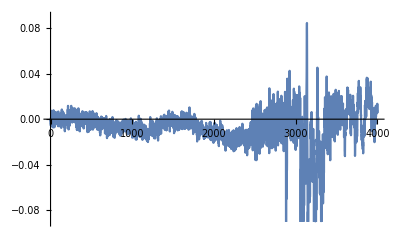

```mathematica
ListLinePlot[Take[utt354[[1]],{17000*2,17000*2+(2000*2)}], PlotRange->{-0.09,0.09}]
```

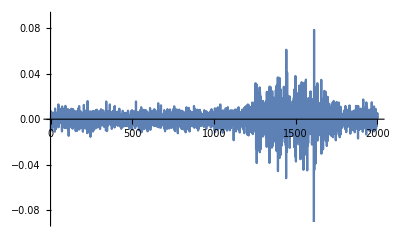

```mathematica
ListLinePlot[Take[singleSampleDelta,{17000,19000}], PlotRange->{-0.09,0.09}]
```

```mathematica
utt354[[1]]
```

{0.0110172,0.00735496,0.00512711,0.00564592,0.00457778,0.000183111,0.00784326,0.00271615,220484,0.0172124,0.0162358,0.0202033,0.0184942,0.018952,0.016419,0.0195624,0.0195624}
 |  |  |  |

## A Formula to output a binary string denoting points in the signal that are novel at a given resolution

Signal will be detected pretty much as per the foundations of Shannon information theory i.e. elements that statistically stand out are hints that a signal is present.

Zero deltas are definitely not signals

Deltas above the amplitude resolution of the human ear are potential signals

Persisting deltas are even more potentially signals

Deltas within a given resolution band are the same signal and not a new signal

New signals are detected when deltas fall into another resolvable resolution band

Fatigue results in a signal blackout after the fatiguing signal for all signal candidates in the same resolution band for a specified transduction fatigue time. All 1’s within the blackout band are therefore still novel rather than a repeat of the same signal.

New signals always reset the blackout window and the blackout threshold in relation to their own delta

If no new signal observed after blackout period then threshold reset to zero. this way a
-- Continuous signal like silence should be a set of evenly spaced 1's
-- Background noise is like a smooth flat raised broad area
-- Spoken sound signal tends to be shorter lived (50ms to 300ms) and a taller, more jaggered hill.

Contour relief can be created through deltas of deltas with thier own thresholds being stacked on top of the bitstring represnting the original deltas.

Further higher level deltas can be created until no signal is observed.

The third dimension is created by partitioning at the next mell-bank defined time resolution and repeating the process.

We end up with a 13 lane wide 3d terrain.

need to
- determine the 13 mell bank ranges of the sample windows from the highest resolution window 
- determine how to detect that deltas are below noise (e.g. magnitude is way below that of signal at the sample window wavelength)
- what to do with outlier deltas... maybe apply correction and keep that as a prediction for the next window. If the prediction holds for a while we may have a new symbol
- what to do when deltas are haphazardly different? consider double delta? Maybe consider the larger window delta as this may imply a groundswell?
- when if ever are double deltas useful?
- For larger windows we need to reduce the deltas to the same number of points as the highest resolution window. Can do this using the NestWhiling of the ReducePartitionDelta function in the asr-research-more notebook?

## More Notes

- Correlation between windows is an indication of signal between those windows.
- constant corellation within certain thresholds => Nothing is happening
- constant slope correlation means a signal is growing/deminishing in magnitude at the rate of the slope
- Higher order changes mean that a signal exists at a lower sample window 
- threshold can be calibrated using the noise

## Playing about

devide list into 2 clusters and replace elements with the cluster number

```mathematica
ClusteringComponents[{1,3,4,5,6,7,8}, 2]
```

{1,1,1,1,2,2,2}

```mathematica
{{1,2,3},{4,5,6}}[[2,2]]
```

5

```mathematica
{a,b,a,b,a,b,a,b,a,b,c}/.{PatternSequence[x_,y_]..}->x+y
```

{a,b,a,b,a,b,a,b,a,b,c}